```mathematica
(* TO APPLY THE LOAD RAMP THE TIME INTERVAL IS~27 s*)
```

```mathematica
(* EVALUATION OF THE TIME INTERVAL TO EXECUTE A LOAD CYCLE IN RAMP *)
```

-Graphics-   -Graphics-

```mathematica
delay=0.05;gap=.755;interval=0.005;period=0.02011;freq=49;level=10;inter=20;
```

```mathematica
volt[voltpic_,freq_,time_]:=voltpic Sin[2 Pi freq time]
```

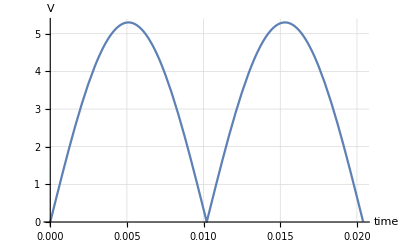

```mathematica
Plot[Abs[volt[5.30,49,t]],{t,0,.0204},GridLines->Automatic,AxesLabel->{"time","V"}]
```

```mathematica
gap/interval
```

151.

```mathematica
time1=252 period+level;
```

```mathematica
time2=(252-2) delay;
```

```mathematica
time1+time2
```

27.5677

```mathematica
(* THIS IS COMPATIBLE WITH THE TIME MEASURED FROM THE STOPWATCH.*)
```

## Thrust Tests

Motors

Anoel 
Racestar BR2205 - 2600KV
Surpass C 2836 - 1120KV

## Introduction

ClearAll["Global`*"]
ClearSystemCache[]

Datasets

0_anoel_teste_linear_ramp_plus75percent_apc3d_945rlh.txt
0_racestar_teste_linear_ramp_plus75percent_apc4d_944sfr.txt
0_surpress_teste_linear_ramp_plus75percent_apc3d_54rrh.txt
0_surpress_teste_linear_ramp_plus75percent_apc3d_63rrh.txt
0_surpress_teste_linear_ramp_plus75percent_apc3d_945rlh.txt
0_surpress_teste_linear_ramp_plus75percent_apc4d_944sfr.txt
0_surpress_teste_linear_ramp_plus75percent_tmotor4d_94.txt

motors={Anoel,Racestar,Surpass};
propellers={apc3d_945rlh,apc4d_944sfr,apc3d_63rrh,apc3d_54rrh,tmotor4d_94};

## Function to aquisition and pre-processing the dataset

```mathematica
dataimport[tagOS_(*W_indows or L_inux*),motor_,propeller_]:=Import[FileNameJoin[{NotebookDirectory[],If[TemplateApply["``",tagOS]=="W",TemplateApply["0_``_teste_linear_ramp_plus75percent_``.txt",{motor,propeller}],If[TemplateApply["``",tagOS]=="L",TemplateApply["0_``_teste_linear_ramp_plus75percent_``.txt",{motor,propeller}]]]}],"Data"]
```

```mathematica
motors={"Anoel","Racestar","Surpass"};
propellers={"APC3D_945RLH","APC4D_944SFR","APC3D_63RLH","APC3D_54RLH","TMotor4D_94"};
```

```mathematica
dropdata[dataset_]:=Transpose[{Transpose[dataset][[2]],Transpose[dataset][[5]]}]
```

```mathematica
dataset1=dropdata[dataimport[W,motors[[1]],propellers[[1]]]];
dataset2=dropdata[dataimport[W,motors[[2]],propellers[[2]]]];
dataset3=dropdata[dataimport[W,motors[[3]],propellers[[1]]]];
dataset4=dropdata[dataimport[W,motors[[3]],propellers[[2]]]];
dataset5=dropdata[dataimport[W,motors[[3]],propellers[[3]]]];
dataset6=dropdata[dataimport[W,motors[[3]],propellers[[4]]]];
dataset7=dropdata[dataimport[W,motors[[3]],propellers[[5]]]];
```

## Generating Results

### Graphics Functions

```mathematica
(*Pulso [0,755]*)
(* Incluir as RPM*)
```

```mathematica
grafmotorandpropeller[dataset_,motor_,propeller_]:=ListPlot[Transpose[{Table[i,{i,0,Length[Transpose[dataset][[2]]]-1}] deltat,Transpose[dataset][[2]] 9.80665}],Joined->True,GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->Style[(*StringTemplate["Curva motor:`` -  hélice: ``" ][motor][]*)TemplateApply["Motor: ``/ Hélice: ``/ Pulso [0,750]",{motor,propeller}],FontSize->20],AxesStyle->Directive[FontFamily->"Times",18],LabelStyle->Directive[(*FontFamily->"Times",*)Black,Bold],(*FrameLabel->{"ϵ","σ (MPa)"},*)AxesLabel->{Style["Tempo (s)",18,Bold,Black],Style["Empuxo (N)",18,Bold,Black]},Background->LightGray]
```

graf1 => base = 100 amostras (~17) - crista 45 amostras (10 s)
graf2 => base = 100 amostras (~17) - crista 42 amostras (10 s) 
graf3 => base = 40 amostras (~17) - crista 10 amostras (10 s)
graf4 => base = 100 amostras (~17) - crista 50 amostras (10 s) 
graf5 => base = 92,5 amostras (~17) - crista 42,5 amostras (10 s) 
graf6 => base = 95 amostras (~17) - crista 40 amostras (10 s) 
graf7 => base = 97,5 amostras (~17) - crista 42,5 amostras (10 s)

```mathematica
m1=(100+100+100+92.5+95+97.5)/6;
m2=(45+42+50+42.5+40+42.5)/6;
delta1=27/(m1)
delta2=10/(m2)
deltat=(delta1+delta2)/2
```

0.276923

0.229008

0.252965

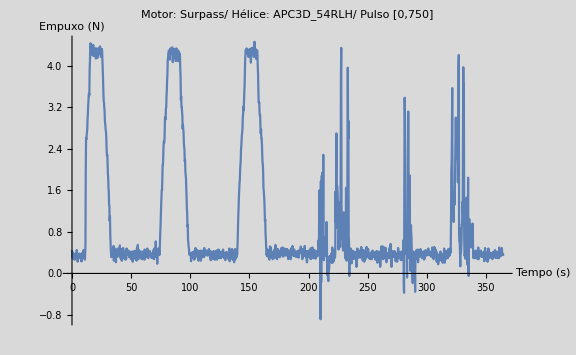

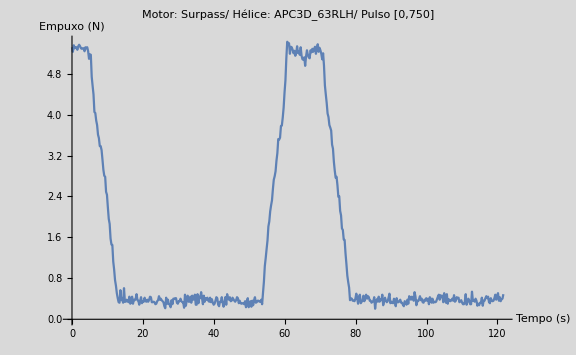

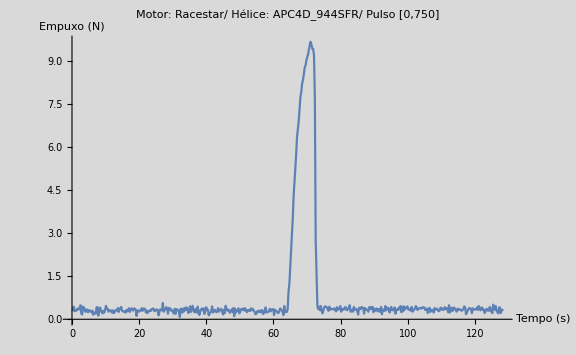

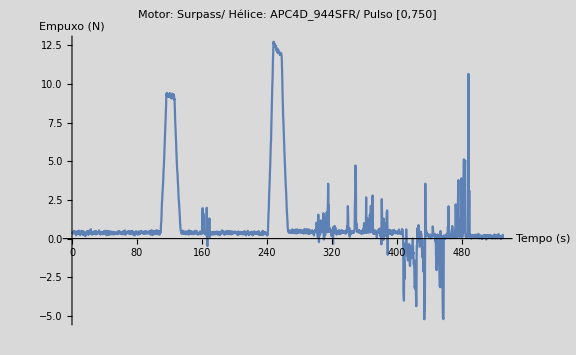

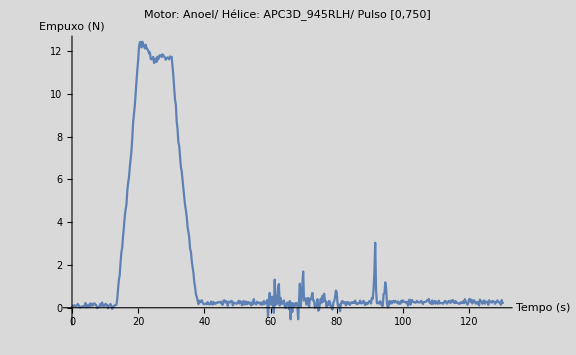

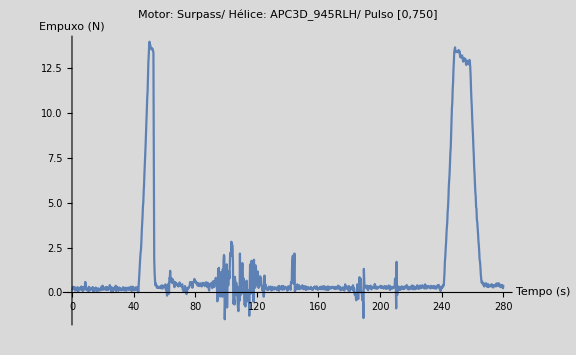

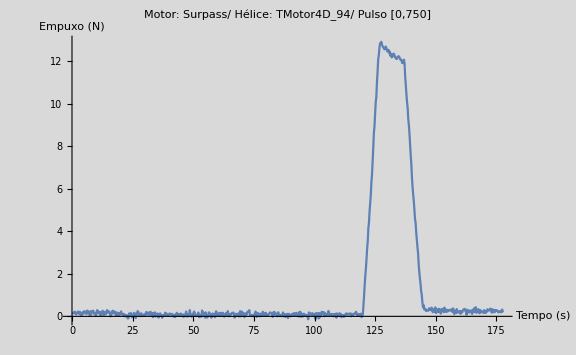

```mathematica
graf1=grafmotorandpropeller[dataset6,motors[[3]],propellers[[4]]]
graf2=grafmotorandpropeller[dataset5,motors[[3]],propellers[[3]]]
graf3=grafmotorandpropeller[dataset2,motors[[2]],propellers[[2]]]
graf4=grafmotorandpropeller[dataset4,motors[[3]],propellers[[2]]]
graf5=grafmotorandpropeller[dataset1,motors[[1]],propellers[[1]]]
graf6=grafmotorandpropeller[dataset3,motors[[3]],propellers[[1]]]
graf7=grafmotorandpropeller[dataset7,motors[[3]],propellers[[5]]]
```